```mathematica
ϵ=0.32;
κ=1.7;
δ=0.33;
B0=5.3;
I0=15;
A=-0.155;
α=ArcSin[δ];
```

```mathematica
Psi1[x_,y_]:=1
Psi2[x_,y_]:=x^2
Psi3[x_,y_]:=y^2 - x^2  Log[x]
Psi4[x_,y_]:=x^4 - 4 x^2 y^2 
Psi5[x_,y_]:=2 y^2 - 9 y^2 x^2 +3 x^4 Log[x] - 12 x^2 y^2 Log[x]
Psi6[x_,y_]:=x^6 - 12 x^4 y^2 + 8 x^2 y^4
Psi7[x_,y_]:=8 y^6 - 140 y^4 x^2 + 75 y^2 x^4 - 15 x^6 Log[x] + 180 x^4 y^2 Log[x] -  120 x^2 y^4 Log [x]
N1=-(1+α)^2/(ϵ κ^2 );
N2=(1-α)^2/(ϵ κ^2);
N3=-κ/(ϵ Cos[α]^2);
```

```mathematica
Psi[x_,y_]:=x^4/8 + A ((1/2)x^2 Log[x] - x^4/8 ) + c1 Psi1[x,y]+ c2 Psi2[x,y]+ c3 Psi3[x,y]+ c4 Psi4[x,y]+ c5 Psi5[x,y]+ c6 Psi6[x,y]+ c7 Psi7[x,y]
```

```mathematica
F1:=Psi[1+ϵ,0]
F2:=Psi[1-ϵ,0]
F3:=Psi[1-δ ϵ,κ ϵ]
PsiX[x_,y_]:=D[Psi[x,y],x]
PsiY[x_,y_]:=D[Psi[x,y],y]
PsiYY[x_,y_]:=D[D[Psi[x,y],y],y]
PsiXX[x_,y_]:=D[D[Psi[x,y],x],x]
F4:=PsiX[x,y]/.{x-> 1-δ ϵ,y-> κ ϵ}
F5:=PsiYY[x,y]+N1 PsiX[x,y]/.{x-> 1+ϵ,y-> 0}
F6:=PsiYY[x,y]+N2 PsiX[x,y] /.{x-> 1-ϵ,y-> 0}
F7:=PsiXX[x,y] + N3 PsiY[x,y] /.{x-> 1-δ ϵ ,y-> κ ϵ}
```

```mathematica
Csol=NSolve[{F1==0,F2==0,F3==0,F4==0,F5==0,F6==0,F7==0},{c1,c2,c3,c4,c5,c6,c7}]
```

{{c1→0.0527261,c2→-0.229077,c3→0.031926,c4→-0.00555385,c5→-0.0145307,c6→0.00333972,c7→0.000137384}}

```mathematica
PsiFinal[x_,y_]:=Psi[x,y]/.Csol
```

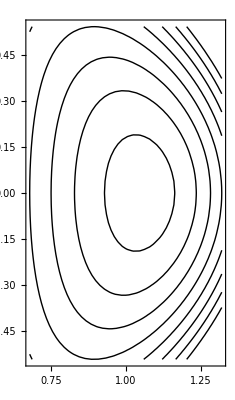

```mathematica
ContourPlot[PsiFinal[x,y],{x,1-ϵ,1+ϵ},{y,-κ ϵ,κ ϵ},AspectRatio->Automatic,ContourShading->None]
```